Plot frequency response of a delay-and-sum beamforming microphone array
Rowan Sharman
Shell TechWorks
2018

```mathematica
minfreq=100;
maxfreq =10000;
vSound=34300;

micDists={1,7,13,19}; (*cm from source*)

getSum[f_]:=
Module[{func=f},
intersects={};
For[i=1,i≤ Length[micDists],i++,
AppendTo[intersects,f /. t->micDists[[i]]];
];
Total[intersects]
]

getMax[f_,fr_]:=
Module[{func=f,freq=fr},
wavelength=vSound/freq;
out=Maximize[getSum[f1/.wl->wavelength],t0];
out[[1]]/Length[micDists]
]

f1=Sin[t*((2*Pi)/wl)+t0];

p=Plot[getMax[f1,frequency],{frequency,minfreq,maxfreq}];

(***********************************************)
```

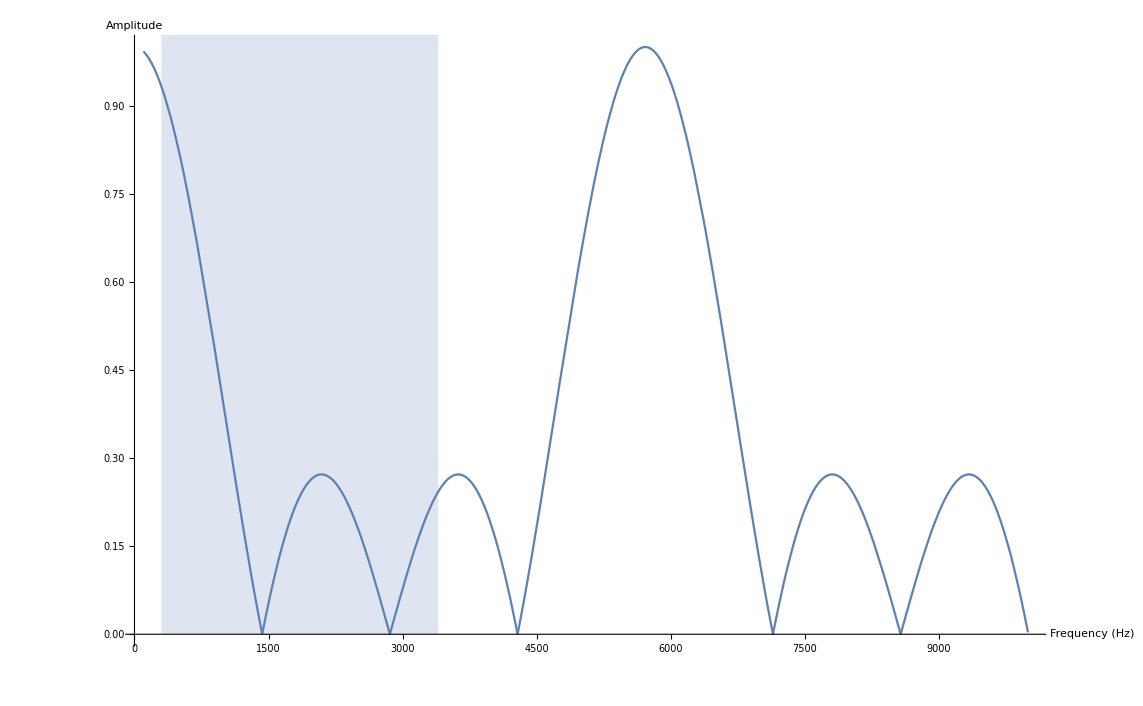

```mathematica
(*Frequency band of interest to highlight*)
minFreqImportant=300;
maxFreqImportant=3400;

region=Plot[2,{f,minFreqImportant,maxFreqImportant},Filling->Axis];
Show[{p,region},AxesOrigin->{0,0},PlotRange->{{minfreq,maxfreq},{0,1}},AxesLabel->{"Frequency (Hz)","Amplitude (linear scale)"}]
```